```mathematica
Clear["Global`*"];
SeedRandom[0];
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<"Sampler2`";
STEPS=3;
CHAINS=3;
```

```mathematica
σ=.01;
U[x_,y_]=1/(2 σ^2)(√(x^2+y^2)-10)^2;
dU[x_,y_]=GradientG[U[x,y],{x,y}];
ddU[x_,y_]=HessianH[U[x,y],{x,y}];
getΣ[x_,y_,r_]:=Module[{Σ=ddU[x,y],ve,e,s},
ve=Eigenvectors[Σ];
e=Eigenvalues[Σ];
s=Sign[e];
Transpose[ve].DiagonalMatrix[s Abs[e]^r].ve];
K[v_,w_,x_,y_,r_]:=Module[{Σ},
Σ=getΣ[x,y,r];
1/2{v,w}.LinearSolve[Σ,{v,w}]];
dKdp[v_,w_,x_,y_,r_]:=Module[{Σ},
Σ=getΣ[x,y,r];
LinearSolve[Σ,{v,w}]];
```

```mathematica
levels=N[Table[i/2,{i,0,2}]];
```

```mathematica
QS=hmc2[U,dU,K,dKdp,2,5000,10000,{},levels];
```

1001136620.0.5828250.4369540.5117723.67822{1,4}{1,4}{0.000228762,0.000789747,0.000156247}{3480.65,136624.,4.75723×10^7}0.000789747

2002267.2892.030590.4518120.4804052.187291{1,2,3}{1,4}{0.000539408,0.00399175,0.0000108347}{269.477,2496.85,3.15234×10^9}0.000539408

30034.19576×10^9-0.1795430.9683440.05483020.6558393{1,3,4}{1,4}{0.00105115,0.0244132,8.14027×10^-6}{135.128,194.909,4.61534×10^9}8.14027×10^-6

400492.63220.5745610.4624190.4885431.111682{1,4}{1,3}{0.00225324,0.0633215,1.97845×10^-7}{17.8744,93.7439,7.10297×10^12}0.0633215

500523.11081.022280.6831310.2958380.6877421{1}{3}{0.0020484,0.0523319,2.00863×10^-8}{23.7986,88.816,5.69513×10^14}0.0020484

60065.69513×10^140.5075690.7506310.3312830.463283{1}{3}{0.0020484,0.0523319,2.00863×10^-8}{23.7986,88.816,5.69513×10^14}2.00863×10^-8

700787.88011.63310.9927130.01262210.9358542{1}{3}{0.0020484,0.0523319,2.00863×10^-8}{23.7986,88.816,5.69513×10^14}0.0523319

800822.41121.088050.6958490.4516681.387321{1}{3}{0.0020484,0.0523319,2.00863×10^-8}{23.7986,88.816,5.69513×10^14}0.0020484

90095.69513×10^140.118440.4711880.4890340.1025053{1}{3}{0.0020484,0.0523319,2.00863×10^-8}{23.7986,88.816,5.69513×10^14}2.00863×10^-8

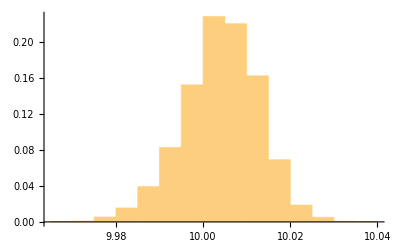

```mathematica
QS1=Table[QS[[i]],{i,1,Length[QS],CHAINS}];
QS2=Table[QS[[i]],{i,2,Length[QS],CHAINS}];
QS3=Table[QS[[i]],{i,3,Length[QS],CHAINS}];
Histogram[√(QS[[;;,1]]^2+QS[[;;,2]]^2),Automatic,"Probability"]
```

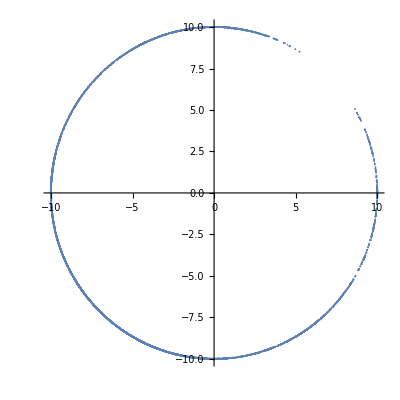

```mathematica
ListPlot[QS,AspectRatio->1]
```